Imagen

```mathematica
img=Image[-Graphics-];
ImageDimensions[img]   (*{980,980}*)
ImageChannels[img]     (*3*)
```

{980,980}

3

Re dimensionando la imagen

```mathematica
gris=ImageResize[ColorConvert[RemoveAlphaChannel[img],"Grayscale"],{400,400}];
ImageChannels[gris]    (*1*)

X=ImageData[gris,"Real"];
Dimensions[X]          (*{400,400}*)
```

1

{400,400}

```mathematica
img
```

-Graphics-

```mathematica
Dimensions[X]
```

{400,400}

Matriz Centrada

```mathematica
(* ---------------------------------------------------------------
   PASO 2. Centrar: restar la media de cada columna
   --------------------------------------------------------------- *)
{n,m}=Dimensions[X]     (*{400,400};ahora n=400 y m=400*)

mu=Mean[X];              (*vector de 400 medias,una por columna*)
muMat=ConstantArray[mu,n];
Xc=X-muMat;
```

{400,400}

Comprobación de la Media cerca de cero

```mathematica
Dimensions[muMat]          (*{400,400}*)
Max@Abs[Mean[Xc]]          (* ~10^-16:cada columna tiene media cero*)
```

{400,400}

2.86021×10^-15

Matriz de Covarianza

{400,400}

1.13798×10^-15

62.4332

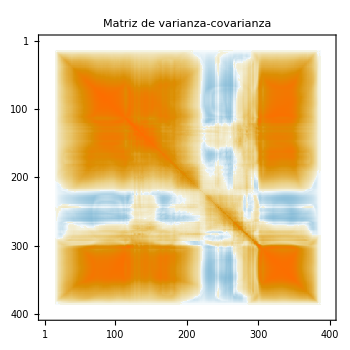

```mathematica
(* ---------------------------------------------------------------
   PASO 3. Matriz de varianza-covarianza (m × m)
   C = Xc^T . Xc / (n - 1)
   --------------------------------------------------------------- *)
covM=Transpose[Xc].Xc/(n-1);

Dimensions[covM]                 (*{400,400}*)
Max@Abs[covM-Covariance[X]]    (* ~10^-16*)

varianzaTotal=Tr[covM]         (* ≈62.43*)

MatrixPlot[covM,PlotLabel->"Matriz de varianza-covarianza",ImageSize->350]
```

Obtención de valores y vectores propios

```mathematica
{lambdas,vecs}=Eigensystem[covM];
orden=Ordering[lambdas,All,Greater];
lambdas=Chop[lambdas[[orden]]];
W=Transpose[vecs[[orden]]];

{Norm[covM.W-W.DiagonalMatrix[lambdas]],Norm[Transpose[W].W-IdentityMatrix[m]]}   (*ambos~10^-13*)

{Total[lambdas],varianzaTotal}                  (*iguales, ≈62.43*)
```

{3.55633×10^-14,3.74787}

{62.4332,62.4332}

CP | λ | % var. | % acum.
1 | 37.74 | 60.45 | 60.45
2 | 5.741 | 9.196 | 69.64
3 | 3.438 | 5.507 | 75.15
4 | 2.545 | 4.077 | 79.23
5 | 2.048 | 3.28 | 82.51
6 | 1.22 | 1.954 | 84.46
7 | 1.079 | 1.728 | 86.19
8 | 0.7859 | 1.259 | 87.45
9 | 0.5769 | 0.924 | 88.37
10 | 0.523 | 0.8376 | 89.21

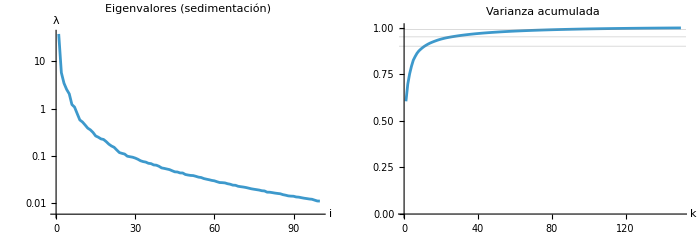

Umbral | Componentes
0.9 | 12
0.95 | 26
0.99 | 88

```mathematica
(* ---------------------------------------------------------------
   PASO 5. Varianza explicada
   --------------------------------------------------------------- *)
proporcion = lambdas/Total[lambdas];
acumulada = Accumulate[proporcion];

TableForm[
 Table[{i, NumberForm[lambdas[[i]], 4], 
   NumberForm[100 proporcion[[i]], 4], 
   NumberForm[100 acumulada[[i]], 4]}, {i, 1, 10}],
 TableHeadings -> {None, {"CP", "λ", "% var.", "% acum."}}]

GraphicsRow[{
  ListLogPlot[lambdas[[;; 100]], Joined -> True, 
   PlotLabel -> "Eigenvalores (sedimentación)", 
   AxesLabel -> {"i", "λ"}],
  ListLinePlot[acumulada[[;; 150]], PlotRange -> {0, 1}, 
   GridLines -> {None, {0.9, 0.95, 0.99}}, 
   PlotLabel -> "Varianza acumulada", AxesLabel -> {"k", ""}]
  }, ImageSize -> 700]

Table[{p, First@FirstPosition[acumulada, _?(# >= p &)]}, 
  {p, {0.90, 0.95, 0.99}}] // 
 TableForm[#, TableHeadings -> {None, {"Umbral", "Componentes"}}] &
```

Proyección y reconstrucción

```mathematica
(* ---------------------------------------------------------------
   PASO 6. Proyección (puntajes) y reconstrucción
   T = Xc . W_k            (n × k)  datos en el nuevo sistema
   X_k = T . W_k^T + μ       (n × m)  imagen reconstruida
   --------------------------------------------------------------- *)
puntajes[k_] := Xc . W[[All, ;; k]];
reconstruir[k_] := 
  Clip[puntajes[k] . Transpose[W[[All, ;; k]]] + muMat, {0., 1.}];
errorRel[k_] := Norm[X - reconstruir[k], "Frobenius"]/Norm[Xc, "Frobenius"];

Grid[Partition[
  Table[Labeled[Image[reconstruir[k], ImageSize -> 180],
    Column[{Row[{"k = ", k}],
      Row[{NumberForm[100 acumulada[[k]], 3], " % de varianza"}],
      Row[{"error: ", NumberForm[errorRel[k], 3]}]}, Alignment -> Center]],
   {k, {2, 5, 12, 26, 50, 88}}], 3], Spacings -> {2, 2}]
```

-Graphics-k = 2
69.6 % de varianza
error: 0.546 | -Graphics-k = 5
82.5 % de varianza
error: 0.407 | -Graphics-k = 12
90.6 % de varianza
error: 0.297
-Graphics-k = 26
95.1 % de varianza
error: 0.213 | -Graphics-k = 50
97.5 % de varianza
error: 0.148 | -Graphics-k = 88
99. % de varianza
error: 0.0909

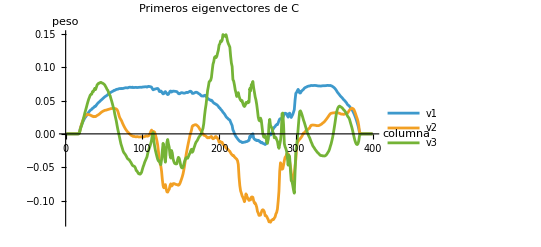

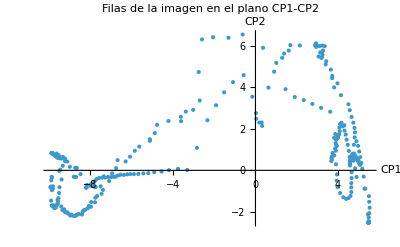

```mathematica
(* ---------------------------------------------------------------
   PASO 7. Las direcciones principales
   Cada eigenvector es un "perfil horizontal" de 400 valores
   --------------------------------------------------------------- *)
ListLinePlot[Table[W[[All, i]], {i, 1, 3}], 
 PlotLegends -> {"v1", "v2", "v3"}, 
 PlotLabel -> "Primeros eigenvectores de C", 
 AxesLabel -> {"columna", "peso"}]

(* Primeros dos puntajes: cada punto es una fila de la imagen *)
ListPlot[puntajes[2], AxesLabel -> {"CP1", "CP2"}, 
 PlotLabel -> "Filas de la imagen en el plano CP1-CP2"]
```

```mathematica
(* ---------------------------------------------------------------
   PASO 8. Exploración interactiva
   --------------------------------------------------------------- *)
Manipulate[
 Row[{Image[reconstruir[k], ImageSize -> 300],
   Column[{
     Row[{"Varianza explicada: ", NumberForm[100 acumulada[[k]], 4], " %"}],
     Row[{"Error relativo: ", NumberForm[errorRel[k], 3]}]}]}, "  "],
 {{k, 12, "componentes"}, 1, 200, 1, Appearance -> "Labeled"},
 SaveDefinitions -> True]
```